```mathematica
SetDirectory["/home/dimas/Física/2 Mestrado/Artigos/JCAP bouncing"]
```

/home/dimas/Física/2 Mestrado/Artigos/JCAP bouncing

## I - Symmetric bounce

```mathematica
Clear["Global`*"]
```

```mathematica
a=am*ⅇ^(h1*t^2/2)
```

am ⅇ^((h1 t^2)/2)

```mathematica
H=D[a,t]/a
```

h1 t

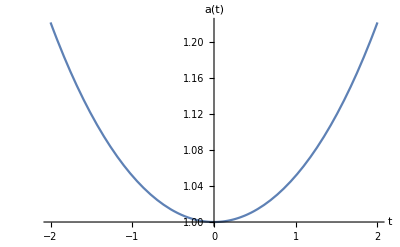

```mathematica
h1=0.1;am=1;pa=Plot[a,{t,-2,2},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aI.pdf",pa]
```

aI.pdf

#### System of ODE’s

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{(0.2+0.06 t^2) F[t]+0.5 t F'[t]+F''[t]==0,0.6+0.12 t^2+0.3 t X'[t]+X''[t]==0,0.3 t Y'[t]+Y''[t]==X'[t]^2,0.3 t V'[t]+1/Y'[t]6 (0.1+0.02 t^2) (F'[t]-U'[t])+V''[t]==0,U'[t]+2 V[t] X'[t]==0}

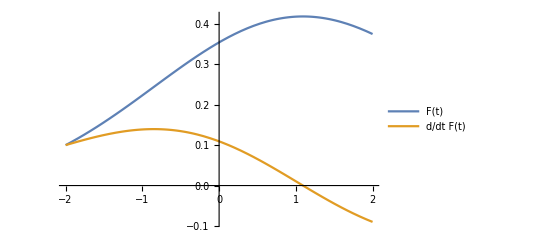
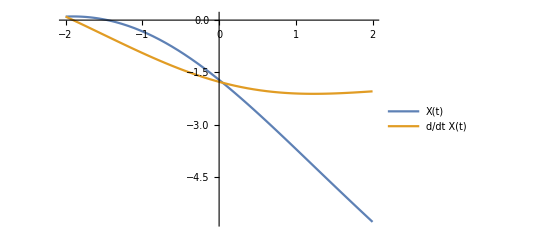
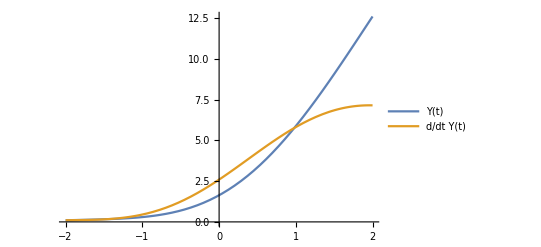
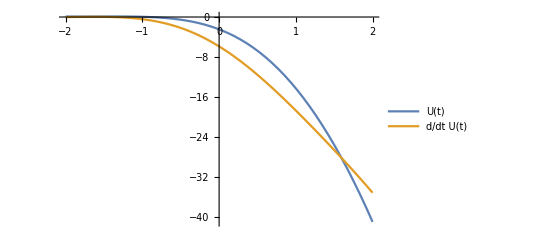
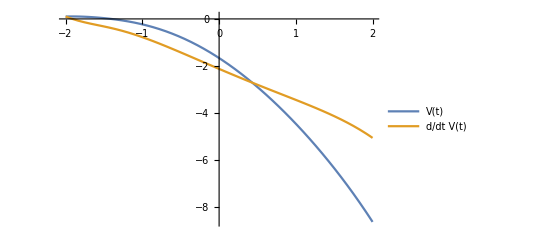

```mathematica
Clear[F,X,Y,U,V];ti=-2;z=0.1;sol=NDSolve[{simp,F[ti]==z,F'[ti]==z,X[ti]==z,X'[ti]==z,Y[ti]==z,Y'[ti]==z,V[ti]==z,V'[ti]==z,U[ti]==z},{F[t],X[t],Y[t],U[t],V[t]},{t,-2,2}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[1]][[i]][[2]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-2,2},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

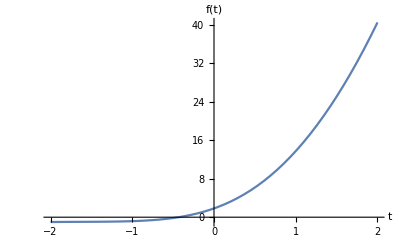

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-2,2}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["ftI.pdf",pf]
```

ftI.pdf

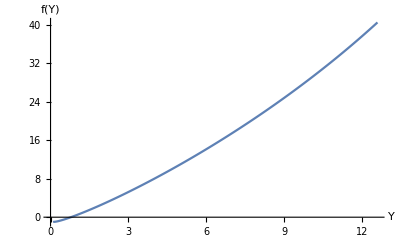

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYI.pdf",line]
```

fYI.pdf

## II - Oscillatory Bounce

```mathematica
Clear["Global`*"]
```

```mathematica
a=A0*Sin[k*t]^2+c
```

c+A0 Sin[k t]^2

```mathematica
H=D[a,t]/a
```

(2 A0 k Cos[k t] Sin[k t])/(c+A0 Sin[k t]^2)

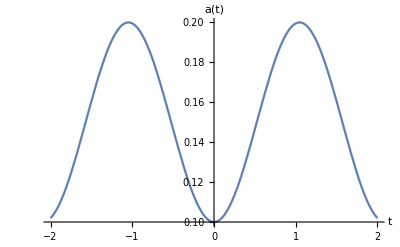

```mathematica
A0=1/10;c=0.1;k=3/2;pa=Plot[a,{t,-2,2},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aII.pdf",pa]
```

aII.pdf

#### System of ODE’s

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{((2.25+13.5 Cos[3 t]-6.75 Cos[6 t]) F[t]+(11.25 Sin[3 t]-1.875 Sin[6 t]) F'[t]+(2.375-1.5 Cos[3 t]+0.125 Cos[6 t]) F''[t])/(1.+Sin[(3 t)/2]^2)^2==0,(40.5 Cos[3 t]-13.5 Cos[6 t]+(6.75 Sin[3 t]-1.125 Sin[6 t]) X'[t]+(2.375-1.5 Cos[3 t]+0.125 Cos[6 t]) X''[t])/(1.+Sin[(3 t)/2]^2)^2==0,(4.5 Sin[3 t] Y'[t])/(1.+Sin[(3 t)/2]^2)+Y''[t]==X'[t]^2,1/((1.+Sin[(3 t)/2]^2)^2 Y'[t])((40.5 Cos[3 t]-13.5 Cos[6 t]) F'[t]+(-40.5 Cos[3 t]+13.5 Cos[6 t]) U'[t]+Y'[t] ((6.75 Sin[3 t]-1.125 Sin[6 t]) V'[t]+(2.375-1.5 Cos[3 t]+0.125 Cos[6 t]) V''[t]))==0,U'[t]+2 V[t] X'[t]==0}

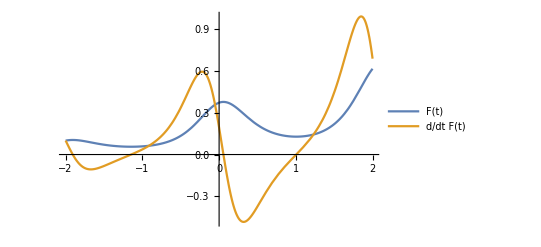
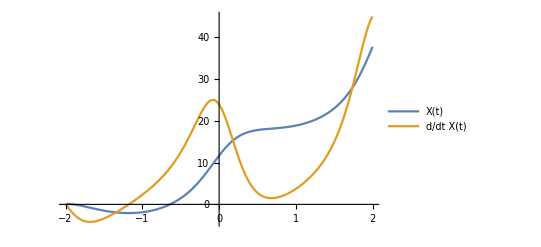
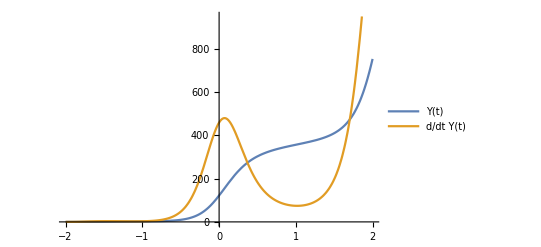
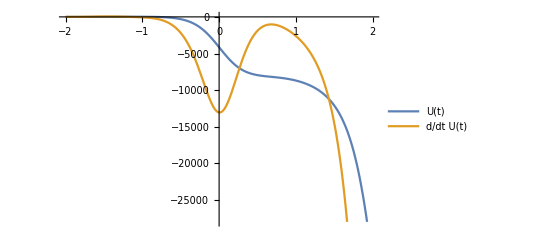
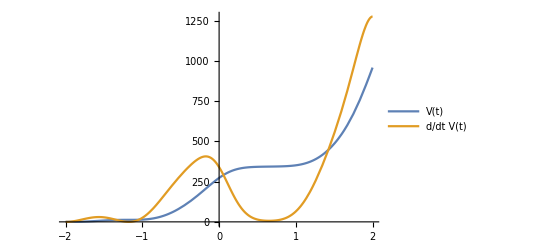

```mathematica
Clear[F,X,Y,U,V];ti=-2;z=0.1;sol=NDSolve[{simp,F[ti]==z,F'[ti]==z,X[ti]==z,X'[ti]==z,Y[ti]==z,Y'[ti]==z,U[ti]==z,V[ti]==z,V'[ti]==z},{F[t],X[t],Y[t],U[t],V[t]},{t,-2,2}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[1]][[i]][[2]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-2,2},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

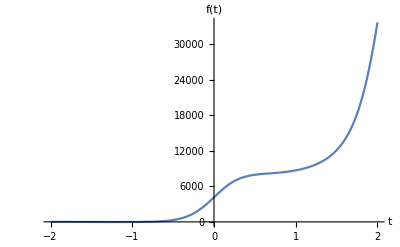

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-2,2}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["ftII.pdf",pf]
```

ftII.pdf

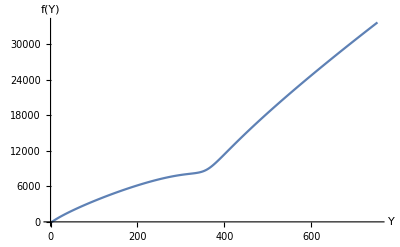

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYII.pdf",line]
```

fYII.pdf

## III - Matter bounce

```mathematica
Clear["Global`*"]
```

```mathematica
a=A0*(3/2ρ*t^2+1)^(1/3)
```

A0 (1+(3 t^2 ρ)/2)^(1/3)

```mathematica
H=D[a,t]/a
```

(t ρ)/(1+(3 t^2 ρ)/2)

0 < ρ << 1 is a critical density from LQC

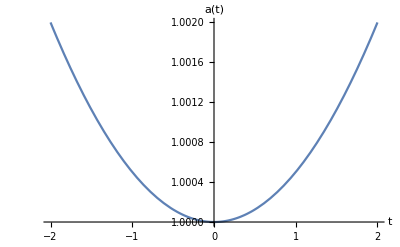

```mathematica
A0=1;ρ=10^(-3);PaI=Plot[a,{t,-2,2},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aIII.pdf",PaI]
```

aIII.pdf

#### System of ODE’s

```mathematica
Clear[F,X,U,V,Y]
```

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{(4 F[t]+10 t F'[t]+(2000+3 t^2) F''[t])/(2000+3 t^2)==0,(12 (2000+t^2)+6 t (2000+3 t^2) X'[t]+(2000+3 t^2)^2 X''[t])/(2000+3 t^2)==0,(6 t Y'[t])/(2000+3 t^2)+Y''[t]==X'[t]^2,(12 (2000+t^2) F'[t]-12 (2000+t^2) U'[t]+(2000+3 t^2) Y'[t] (6 t V'[t]+(2000+3 t^2) V''[t]))/((2000+3 t^2) Y'[t])==0,U'[t]+2 V[t] X'[t]==0}

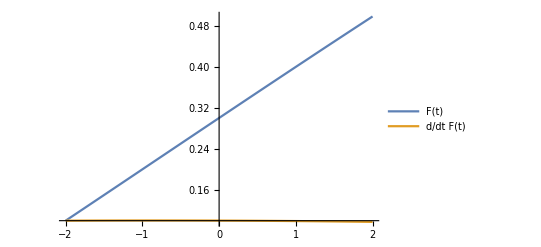
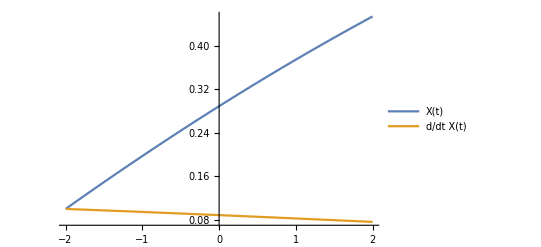
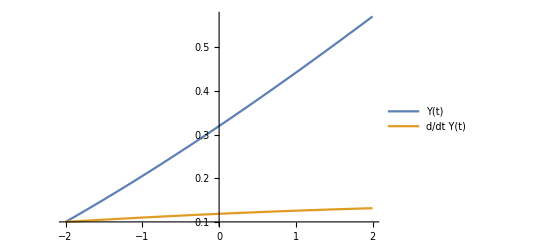
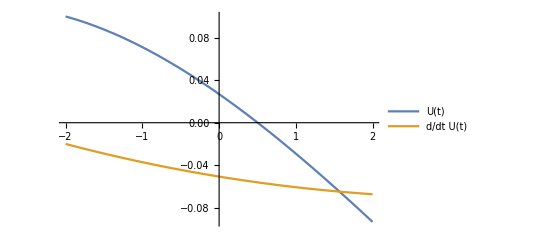
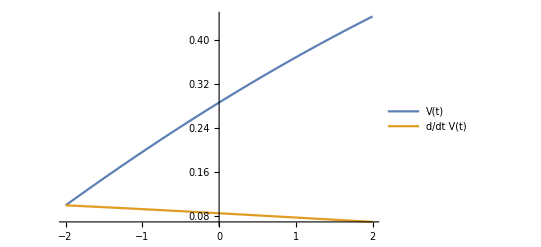

```mathematica
ti=-2;z=0.1;Clear[F,X,Y,U,V];sol=NDSolve[{simp,F[ti]==z,F'[ti]==z,X[ti]==z,X'[ti]==z,Y[ti]==z,Y'[ti]==z,V[ti]==z,V'[ti]==z,U[ti]==z},{F[t],X[t],Y[t],U[t],V[t]},{t,-2,2}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[1]][[i]][[2]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-2,2},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

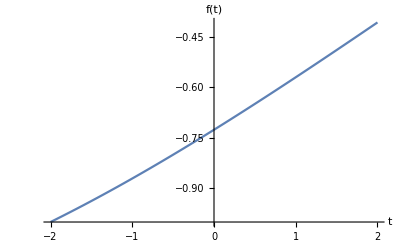

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-2,2}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["ftIII.pdf",pf]
```

ftIII.pdf

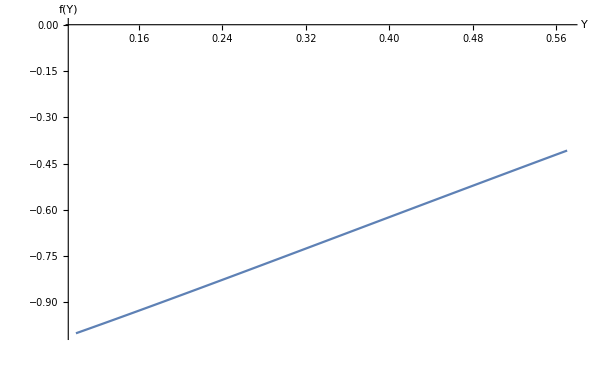

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYIII.pdf",line]
```

fYIII.pdf

## IV - Singularities cosmologies

```mathematica
Clear[γ];a=ⅇ^(t^γ);H=D[a,t]/a;γ=3.78;D[H,{t,2}]/.{t->0}
```

0.

```mathematica
Clear["Global`*"]
```

```mathematica
a=A0*ⅇ^(f0/(α+1)*(t-ts)^(α+1))
```

A0 ⅇ^((f0 (t-ts)^(1+α))/(1+α))

```mathematica
H=D[a,t]/a
```

f0 (t-ts)^α

### α > 1

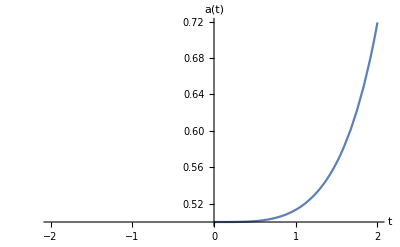

```mathematica
A0=1/2;f0=1/10;α=2.78;ts=0;pa2=Plot[{a},{t,-2,2},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aIV.pdf",pa2]
```

aIV.pdf

#### System of ODE’s

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{3 t^2 (10+t^4) F[t]+25 (t^3 F'[t]+2 F''[t])==0,90 t^2+6 t^6+15 t^3 X'[t]+50 X''[t]==0,3/10 t^3 Y'[t]+Y''[t]==X'[t]^2,3/10 t^3 V'[t]+(3 t^2 (15+t^4) (F'[t]-U'[t]))/(25 Y'[t])+V''[t]==0,U'[t]+2 V[t] X'[t]==0}

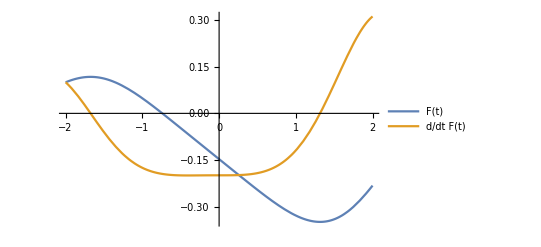
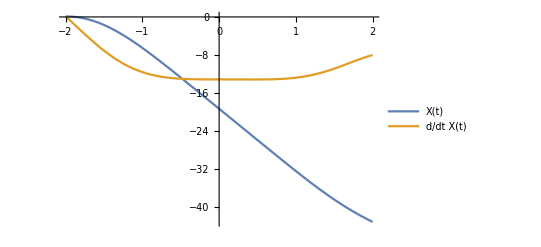
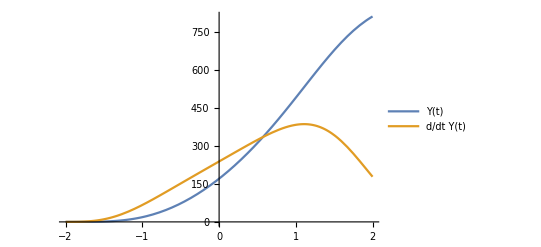
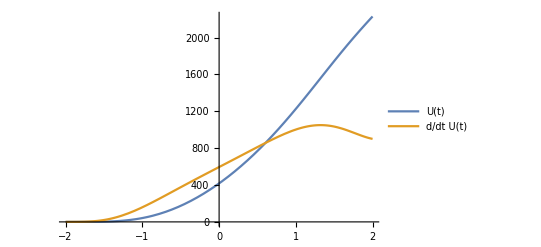
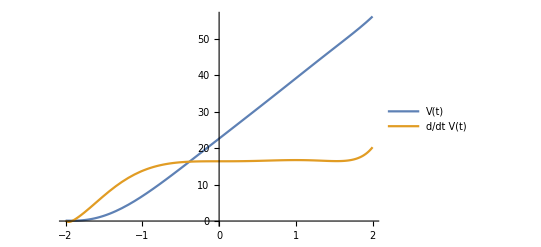

```mathematica
ti=-2;z=0.1;cc={F[ti]==z,X[ti]==z,Y[ti]==z,F'[ti]==z,X'[ti]==z,Y'[ti]==z,V[ti]==z,V'[ti]==z,U[ti]==z};Clear[F,X,Y,U,V];sol=NDSolveValue[{simp,cc},{F[t],X[t],Y[t],U[t],V[t]},{t,-2,2}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[i]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-2,2},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

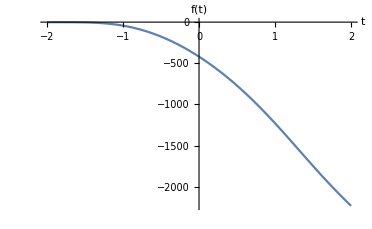

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-2,2}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["ftIV.pdf",pf]
```

ftIV.pdf

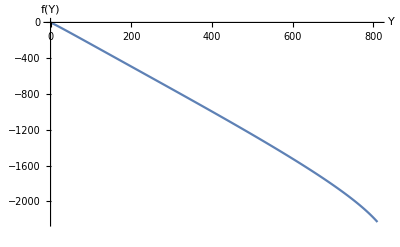

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYIV.pdf",line]
```

fYIV.pdf

## V - Pre-inflationary asymmetric bounce

```mathematica
Clear["Global`*"]
```

```mathematica
a=a0*ⅇ^(-Hb^3*t^3-Hi^2t^2+H0*t)
```

a0 ⅇ^(H0 t-Hi^2 t^2-Hb^3 t^3)

```mathematica
H=D[a,t]/a
```

H0-2 Hi^2 t-3 Hb^3 t^2

```mathematica
Clear[H0,Hb,Hi]
```

```mathematica
Solve[D[a,t]==0,t]
```

{{t→(-Hi^2-√(3 H0 Hb^3+Hi^4))/(3 Hb^3)},{t→(-Hi^2+√(3 H0 Hb^3+Hi^4))/(3 Hb^3)}}

```mathematica
Solve[3 H0 Hb^3+Hi^4==0,H0]
```

{{H0→-Hi^4/(3 Hb^3)}}

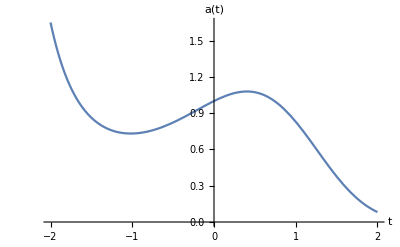

```mathematica
H0=1/3;Hi=1/2;Hb=11/17;a0=1;pa=Plot[a,{t,-2,2},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aV.pdf",pa]
```

aV.pdf

#### System of ODE’s

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{2 (-1/2-(7986 t)/4913) F[t]+6 (-1/3+t/2+(3993 t^2)/4913)^2 F[t]+5 (1/3-t/2-(3993 t^2)/4913) F'[t]+F''[t]==0,6 (-1/2-(7986 t)/4913+2 (-1/3+t/2+(3993 t^2)/4913)^2)+3 (1/3-t/2-(3993 t^2)/4913) X'[t]+X''[t]==0,(1-(3 t)/2-(11979 t^2)/4913) Y'[t]+Y''[t]==X'[t]^2,3 (1/3-t/2-(3993 t^2)/4913) V'[t]+1/Y'[t]6 (-1/2-(7986 t)/4913+2 (-1/3+t/2+(3993 t^2)/4913)^2) (F'[t]-U'[t])+V''[t]==0,U'[t]+2 V[t] X'[t]==0}

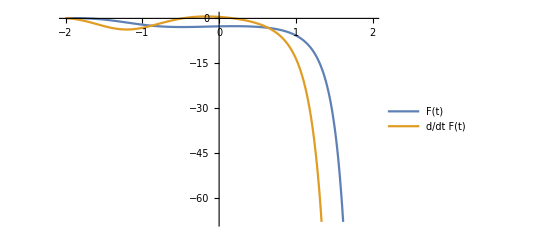
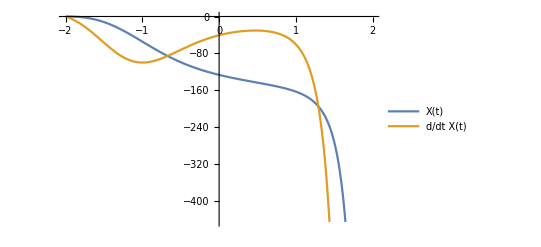
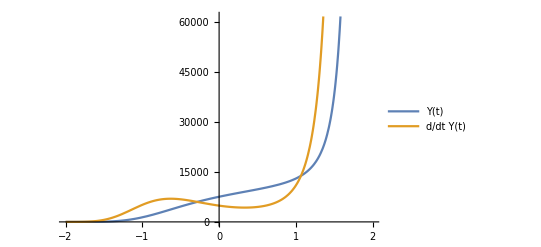
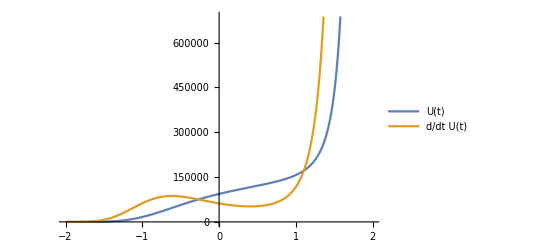
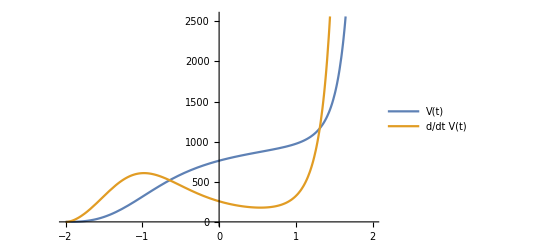

```mathematica
Clear[F,X,Y,U,V];ti=-2;z=0.1;sol=NDSolve[{simp,F[ti]==z,F'[ti]==z,X[ti]==z,X'[ti]==z,Y[ti]==z,Y'[ti]==z,V[ti]==z,V'[ti]==z,U[ti]==z},{F[t],X[t],Y[t],U[t],V[t]},{t,-2,2}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[1]][[i]][[2]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-2,2},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

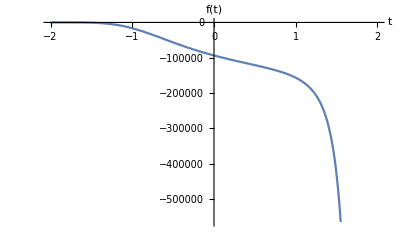

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-2,2}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["ftV.pdf",pf]
```

ftV.pdf

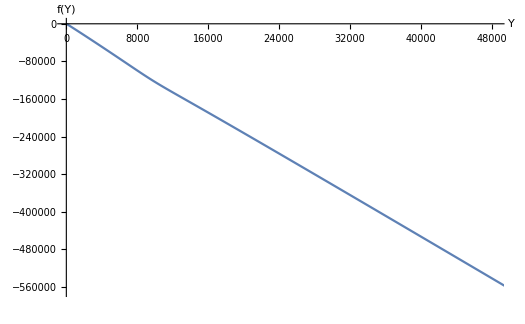

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYV.pdf",line]
```

fYV.pdf